```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

```mathematica
Plot[{1/x^2},{x,1,3},PlotLabels->{1/x^2},PlotRange->{0,1}, Filling->Bottom]
```

-Graphics-

```mathematica
t
```

```mathematica
Integrate[1/x^2,{x,1,t}]
```

ConditionalExpression[1-1/t, Re[t]>0||t∉ℝ]

```mathematica
D[1-1/t,t]
```

1/t^2

```mathematica
t^(-2)
```

1/t^2

```mathematica
(-1)(1/t)-(-1)(1/1)
```

1-1/t

```mathematica
f1[x_]:=1/x^2
f2[x_]:=1/x
S1=List[Table[1/n^2,{n,1,30}]]
```

```mathematica
Plot[{f1[x],f2[x]},{x,1,4.5},PlotStyle->{Red,Blue},PlotLabels->{Style[f1[x],Background->LightYellow],Style[f2[x],Background->LightYellow]}, Background->LightYellow,Filling->Bottom, PlotRange->{0,1},PlotLabel->Style["(1/x) vs (1/x)-squared",FontSize->14,Background->LightYellow],AxesLabel->Style["f(x)",FontSize->14]]
```

-Graphics-

```mathematica
PlotLabels->{Style[f1[x],Background->LightYellow],Style[f2[x],Background->LightYellow]}
```

PlotLabels→{1/x^2,1/x}

```mathematica
Plot[{f3[x]},{x,1,4.5},PlotStyle->{Red},PlotLabels->{Style[f3[x],Background->LightYellow],Style[f2[x],Background->LightYellow]}, Background->LightYellow,Filling->Bottom, PlotRange->{0,1},PlotLabel->Style["(1/x^2)",FontSize->14,Background->LightYellow],AxesLabel->Style["f(x)",FontSize->14]]
```

-Graphics-

```mathematica
f3[x_]:=1/x^2
```

```mathematica
1/L*Integrate[x*Sin[n*x/L],{x,-L,L}]
```

-(2 L (n Cos[n]-Sin[n]))/n^2

```mathematica
Simplify[-(2 L (n Cos[n]-Sin[n]))/n^2]
```

```mathematica
(2 L (-n Cos[n]+Sin[n]))/n^2//DisplayForm
```

(2 L (-n Cos[n]+Sin[n]))/n^2

```mathematica
Integrate[x,{x,-L,L}]
```

0

```mathematica
Integrate[x*Cos[x],x]
```

Cos[x]+x Sin[x]

```mathematica
1/Pi*Integrate[x*Sin[n*x],{x,-Pi,Pi}]
```

(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π)

```mathematica
FullSimplify[(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π)]
```

```mathematica
(2 (-n π Cos[n π]))/(n^2 π)
```

-(2 Cos[n π])/n

```mathematica
(-2 n π Cos[n π])/n^2
```

-(2 π Cos[n π])/n

```mathematica
FullSimplify[(-2 n π Cos[n π]+2 Sin[n π])/n^2]
```

(2 (-n π Cos[n π]+Sin[n π]))/n^2

```mathematica
Integrate[x^2,{x,-Pi,Pi}]
```

(2 π^3)/3

```mathematica
(1/Pi*Integrate[x*Sin[n*x],{x,-Pi,Pi}])^2
```

```mathematica
(-2 n π Cos[n π])^2/(n^4 π^2)
```

(4 Cos[n π]^2)/n^2

```mathematica
(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π)
```

```mathematica
(-2 n π Cos[n π])/(n^2 π)
```

-(2 Cos[n π])/n

```mathematica
n=4
```

4

```mathematica
ClearAll[n]
```

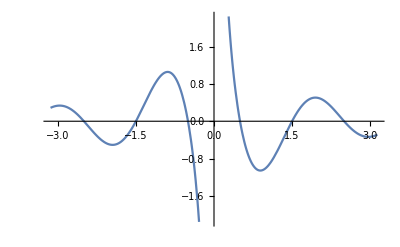

```mathematica
Plot[Cos[x*Pi]/x,{x,-Pi,Pi}]
```

```mathematica
(2 π^3)/3/4//Simplify
```

π^3/6

```mathematica
Cos[n*Pi]^2/n^2
```

Cos[n π]^2/n^2

```mathematica
Table[Cos[n π]^2/n^2,{n,1,20}]
```

{1,1/4,1/9,1/16,1/25,1/36,1/49,1/64,1/81,1/100,1/121,1/144,1/169,1/196,1/225,1/256,1/289,1/324,1/361,1/400}

```mathematica
Series
```